```mathematica
<<FeynCalc`
```

```mathematica
(* ============================================================*)(*HIGGS PORTAL:phi(k1) chi(k2) chi(k3)->chi(p1) chi(p2)*)(**)(*Majorana chi,scalar phi (mass mY),v-bar...u spinor convention*)(*Uses same spinor assignments as vector portal (Dirac-like)*)(*FeynCalc 9.3+handles Majorana cross-term chain reordering*)(**)(*8 direct diagrams:*)(*S-pairing (1-4):chains connect (k2,k3) and (p1,p2)*)(*T-pairing (5-8):chains connect (k3,p2) and (k2,p1)*)(**)(*8 exchange diagrams (9-16):p1<->p2 of direct*)(**)(*Signs:S-pairing=+1,T-pairing=-1*)(*Exchange amplitudes get extra-1 from antisymmetrize*)(**)(*Vertex:V=lams+I lamp GA[5]*)(*Key Majorana property:C V^T C^{-1}=V*)(* ============================================================*)<<FeynCalc`
FCClearScalarProducts[];

(* ============================================================*)
(*KINEMATICS*)
(*phi=Y (mass mY),chi=X (mass mX),r=mX/mY>1*)
(* ============================================================*)
SP[k1,k1]=mY^2;SP[k2,k2]=mX^2;
SP[k3,k3]=mX^2;SP[p1,p1]=mX^2;SP[p2,p2]=mX^2;

SP[k1,k2]=(s12-mY^2-mX^2)/2;
SP[k1,k3]=(s13-mY^2-mX^2)/2;
SP[k1,p1]=(mY^2+mX^2-t1)/2;
SP[k2,p1]=(2 mX^2-t2)/2;
SP[k3,p1]=(2 mX^2-t3)/2;

(*k2.k3 from p2^2=mX^2,using p2=k1+k2+k3-p1*)
SP[k2,k3]=-(s12-mY^2-mX^2)/2-(s13-mY^2-mX^2)/2
+(mY^2+mX^2-t1)/2+(2 mX^2-t2)/2
+(2 mX^2-t3)/2-(mY^2+2 mX^2)/2;

(*p2=k1+k2+k3-p1 cross terms*)
SP[p2,k1]=SP[k1,k1]+SP[k1,k2]+SP[k1,k3]-SP[k1,p1];
SP[p2,k2]=SP[k1,k2]+SP[k2,k2]+SP[k2,k3]-SP[k2,p1];
SP[p2,k3]=SP[k1,k3]+SP[k2,k3]+SP[k3,k3]-SP[k3,p1];
SP[p2,p1]=SP[k1,p1]+SP[k2,p1]+SP[k3,p1]-SP[p1,p1];

(*---NR definitions---*)
sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
EXf=sqrtsNR/2;

NRrules={s12->(mY+mX)^2,s13->(mY+mX)^2,t1->mY^2+mX^2-2 mY EXf,t2->2 mX^2-2 mX EXf,t3->2 mX^2-2 mX EXf};

(* ============================================================*)
(*VERTEX*)
(*phi-chi-chi:V=lambda_s+i lambda_p gamma^5*)
(**)
(*C V^T C^{-1}=V (unchanged under charge conjugation)*)
(*C (GS[P]+mX)^T C^{-1}=-GS[P]+mX (momentum sign flip)*)
(* ============================================================*)
V=lams+I lamp GA[5];

(* ============================================================*)
(*S-PAIRING DIAGRAMS (1-4):sign=+1*)
(**)
(*Wick contraction:(k2,k3) and (p1,p2)*)
(**)
(*v-bar...u spinor assignments (same as vector portal):*)
(*Chain A (k2,k3):v-bar(k2).V.u(k3)*)
(*Chain B (p1,p2):u-bar(p2).V.(GS[P]+mX).V.v(p1)*)
(**)
(*Standard propagators (GS[P]+mX) throughout—no sign flips*)
(* ============================================================*)

(*----Diagram 1 (S1):phi*at q=k2+k3,chi prop on (p1,p2) chain----*)
(*Topology:chi(k2)+chi(k3)->phi*,phi*->chi+phi(k1)->chi(p1)+chi(p2)*)
(*Chain A:single vertex.Chain B:chi prop with P=k2+k3-p1*)
qPhi1=k2+k3;
PX1=k2+k3-p1;
DenPhi1=ExpandScalarProduct[SP[qPhi1,qPhi1]]-mY^2;
DenX1=ExpandScalarProduct[SP[PX1,PX1]]-mX^2;

num1=SpinorVBar[k2,mX].V.SpinorU[k3,mX]*SpinorUBar[p2,mX].V.(GS[PX1]+mX).V.SpinorV[p1,mX];
amp1={num1,DenPhi1 DenX1};

(*----Diagram 2 (S2):phi*at q=k2+k3,chi prop on (p1,p2) chain----*)
(*Same phi*as S1,but phi(k1) emitted from other end*)
(*chi prop P=k1-p1*)
qPhi2=k2+k3;
PX2=k1-p1;
DenPhi2=ExpandScalarProduct[SP[qPhi2,qPhi2]]-mY^2;
DenX2=ExpandScalarProduct[SP[PX2,PX2]]-mX^2;

num2=SpinorVBar[k2,mX].V.SpinorU[k3,mX]*SpinorUBar[p2,mX].V.(GS[PX2]+mX).V.SpinorV[p1,mX];
amp2={num2,DenPhi2 DenX2};

(*----Diagram 3 (S3):phi*at q=p1+p2,chi prop on (k2,k3) chain----*)
(*Topology:chi(k3)+phi(k1)->chi_prop,chi_prop+chi(k2)->phi**)
(*phi*->chi(p1)+chi(p2).chi prop P=k1+k3*)
qPhi3=p1+p2;
PX3=k1+k3;
DenPhi3=ExpandScalarProduct[SP[qPhi3,qPhi3]]-mY^2;
DenX3=ExpandScalarProduct[SP[PX3,PX3]]-mX^2;

num3=SpinorUBar[p2,mX].V.SpinorV[p1,mX]*SpinorVBar[k2,mX].V.(GS[PX3]+mX).V.SpinorU[k3,mX];
amp3={num3,DenPhi3 DenX3};

(*----Diagram 4 (S4):phi*at q=p1+p2,chi prop on (k2,k3) chain----*)
(*phi(k1) absorbed by chi(k2) end.chi prop P=-(k1+k2)*)
qPhi4=p1+p2;
PX4=-(k1+k2);
DenPhi4=ExpandScalarProduct[SP[qPhi4,qPhi4]]-mY^2;
DenX4=ExpandScalarProduct[SP[PX4,PX4]]-mX^2;

num4=SpinorUBar[p2,mX].V.SpinorV[p1,mX]*SpinorVBar[k2,mX].V.(GS[PX4]+mX).V.SpinorU[k3,mX];
amp4={num4,DenPhi4 DenX4};

(* ============================================================*)
(*T-PAIRING DIAGRAMS (5-8):sign=-1*)
(**)
(*Wick contraction:(k3,p2) and (k2,p1)*)
(**)
(*v-bar...u spinor assignments (same as vector portal):*)
(*Chain 1 (k3->p2):u-bar(p2).V.(GS[P]+mX).V.u(k3)*)
(*[natural fermion direction,standard propagator]*)
(*Chain 2 (k2->p1):v-bar(k2).V.(GS[P]+mX).V.v(p1)*)
(*[antifermion direction,standard propagator]*)
(* ============================================================*)

(*----Diagram 5 (T1):phi*at q=k2-p1,chi prop on (k3,p2) chain----*)
(*Chain 1 (k3->p2):phi(k1) and phi*both on this chain*)
(*chi prop P=k2+k3-p1,standard propagator*)
(*Chain 2 (k2->p1):single vertex v-bar(k2).V.v(p1)*)
qPhi5=k2-p1;
PX5=k2+k3-p1;
DenPhi5=ExpandScalarProduct[SP[qPhi5,qPhi5]]-mY^2;
DenX5=ExpandScalarProduct[SP[PX5,PX5]]-mX^2;

num5=SpinorUBar[p2,mX].V.(GS[PX5]+mX).V.SpinorU[k3,mX]*SpinorVBar[k2,mX].V.SpinorV[p1,mX];
amp5={num5,DenPhi5 DenX5};

(*----Diagram 6 (T2):phi*at q=k3-p2,chi prop on (k2,p1) chain----*)
(*Chain 1 (k3->p2):single vertex u-bar(p2).V.u(k3)*)
(*Chain 2 (k2->p1):chi prop P=-(k1+k2),standard propagator*)
qPhi6=k3-p2;
PX6=-(k1+k2);
DenPhi6=ExpandScalarProduct[SP[qPhi6,qPhi6]]-mY^2;
DenX6=ExpandScalarProduct[SP[PX6,PX6]]-mX^2;

num6=SpinorUBar[p2,mX].V.SpinorU[k3,mX]*SpinorVBar[k2,mX].V.(GS[PX6]+mX).V.SpinorV[p1,mX];
amp6={num6,DenPhi6 DenX6};

(*----Diagram 7 (T3):phi(k1) absorbed by chi(k3),phi*connects chains--*)
(*Chain 1 (k3->p2):chi prop P=k1+k3,standard propagator*)
(*Chain 2 (k2->p1):single vertex v-bar(k2).V.v(p1)*)
qPhi7=p1-k2;
PX7=k1+k3;
DenPhi7=ExpandScalarProduct[SP[qPhi7,qPhi7]]-mY^2;
DenX7=ExpandScalarProduct[SP[PX7,PX7]]-mX^2;

num7=SpinorUBar[p2,mX].V.(GS[PX7]+mX).V.SpinorU[k3,mX]*SpinorVBar[k2,mX].V.SpinorV[p1,mX];
amp7={num7,DenPhi7 DenX7};

(*----Diagram 8 (T4):phi(k1) absorbed by chi(p1),phi*connects chains--*)
(*Chain 1 (k3->p2):single vertex u-bar(p2).V.u(k3)*)
(*Chain 2 (k2->p1):chi prop P=k1-p1,standard propagator*)
qPhi8=p2-k3;
PX8=k1-p1;
DenPhi8=ExpandScalarProduct[SP[qPhi8,qPhi8]]-mY^2;
DenX8=ExpandScalarProduct[SP[PX8,PX8]]-mX^2;

num8=SpinorUBar[p2,mX].V.SpinorU[k3,mX]*SpinorVBar[k2,mX].V.(GS[PX8]+mX).V.SpinorV[p1,mX];
amp8={num8,DenPhi8 DenX8};

(* ============================================================*)
(*EXCHANGE AMPLITUDES (9-16):swap p1<->p2 in direct*)
(*These get an extra-1 from Fermi antisymmetrization*)
(* ============================================================*)

(*Momentum swap rule (two-step to avoid conflicts)*)
swapP={p1->ptmp};
swapP2={p2->p1,ptmp->p2};
swapMomenta[expr_]:=expr/. swapP/. swapP2;

(*Generate exchange amplitudes*)
{num9,den9}={swapMomenta[num1],swapMomenta[DenPhi1 DenX1]};
{num10,den10}={swapMomenta[num2],swapMomenta[DenPhi2 DenX2]};
{num11,den11}={swapMomenta[num3],swapMomenta[DenPhi3 DenX3]};
{num12,den12}={swapMomenta[num4],swapMomenta[DenPhi4 DenX4]};
{num13,den13}={swapMomenta[num5],swapMomenta[DenPhi5 DenX5]};
{num14,den14}={swapMomenta[num6],swapMomenta[DenPhi6 DenX6]};
{num15,den15}={swapMomenta[num7],swapMomenta[DenPhi7 DenX7]};
{num16,den16}={swapMomenta[num8],swapMomenta[DenPhi8 DenX8]};

amp9={num9,den9};amp10={num10,den10};
amp11={num11,den11};amp12={num12,den12};
amp13={num13,den13};amp14={num14,den14};
amp15={num15,den15};amp16={num16,den16};

(* ============================================================*)
(*Collect all 16 amplitudes and signs*)
(* ============================================================*)
amps={amp1,amp2,amp3,amp4,amp5,amp6,amp7,amp8,amp9,amp10,amp11,amp12,amp13,amp14,amp15,amp16};

(*Signs:*)
(*Direct S-pairing (1-4):+1*)
(*Direct T-pairing (5-8):-1*)
(*Exchange S-pairing (9-12):-1 (extra-1 from exchange)*)
(*Exchange T-pairing (13-16):+1 (two-1's cancel)*)
signs={+1,+1,+1,+1,-1,-1,-1,-1,-1,-1,-1,-1,+1,+1,+1,+1};

(* ============================================================*)
(*Process one interference term*)
(**)
(*Simplified relative to vector portal:*)
(*-No Lorentz index renaming (no free indices)*)
(*-No polarization sum (phi is scalar)*)
(*-No Contract (no Lorentz tensors)*)
(* ============================================================*)
proc[i_,j_]:=Module[{nI,dI,nJ,dJ,cc,Mij,leftover},{nI,dI}=amps[[i]];
{nJ,dJ}=amps[[j]];
(*Complex conjugate—no index renaming needed*)(*Ensure lams,lamp treated as real*)cc=ComplexConjugate[nJ]/. {Conjugate[lams]->lams,Conjugate[lamp]->lamp};
(*Spin sum:FermionSpinSum replaces u(p)u-bar(p)-> /p+m*)(*For same-pairing:produces product of two traces*)(*For cross-pairing:produces single long trace (automatic)*)(*FCI[] ensures product is in FeynCalc internal form*)(*DiracSimplify canonicalizes Dirac algebra before spin sum*)Mij=FermionSpinSum[DiracSimplify[FCI[nI cc]]]/. DiracTrace->TR;
(*Expand scalar products*)Mij=ExpandScalarProduct[Mij];
(*Force 4D*)Mij=ChangeDimension[Mij,4];
Mij=ExpandScalarProduct[Mij];
(*Diagnostic:check for unresolved Pair objects*)leftover=Cases[Mij,Pair[__],Infinity]//Union;
If[leftover=!={},Print["  WARNING: surviving Pair objects in (",i,",",j,"): ",leftover]];
(*Divide by propagator denominators and apply NR*)Mij=Mij/(dI dJ);
Mij=Mij/. NRrules;
(*Kill Levi-Civita terms:exactly zero in NR limit*)(*(all momenta collinear at threshold)*)Mij=Mij/. Eps[__]->0;
Mij=PowerExpand[Mij]/. mY->mX/r//FullSimplify];

(* ============================================================*)
(*Quick sanity check:diagonal of diagram 7*)
(*(Should match the test script result)*)
(* ============================================================*)
Print["=== Sanity check: proc[7,7] ==="];
test77=proc[7,7];
Print["proc[7,7] = ",test77];
Print[""];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

1/2 (mX^2+mY^2-s12)+1/2 (mX^2+mY^2-s13)

1/2 (mX^2+mY^2-t1)+1/2 (2 mX^2-t2)

=== Sanity check: proc[7,7] ===

proc[7,7] = (4 r^4 (lamp^2+lams^2 (1+4 r)) (lamp^4 (5+6 r)+lams^4 (1+2 r) (5+4 r^2)+2 lamp^2 lams^2 (5+2 r (4+r-2 r^2))))/(mX^2 (1+r)^2 (1+2 r)^2)

```mathematica
(* ============================================================*)
(*Write each term to file,one at a time*)
(*Total:16 diagonal+C(16,2)=16+120=136 terms*)
(* ============================================================*)
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_HP"}];
If[!DirectoryQ[outputDir],CreateDirectory[outputDir]];

(*---Diagonal terms---*)
Do[Print["(",i,",",i,") ..."];
term=proc[i,i];
Put[term,FileNameJoin[{outputDir,"diag_"<>ToString[i]<>"_"<>ToString[i]<>".m"}]];
Clear[term];
Print["  Done."];,{i,1,16}];
```

(1,1) ...

Done.

(2,2) ...

Done.

(3,3) ...

Done.

(4,4) ...

Done.

(5,5) ...

Done.

(6,6) ...

Done.

(7,7) ...

Done.

(8,8) ...

Done.

(9,9) ...

Done.

(10,10) ...

Done.

(11,11) ...

Done.

(12,12) ...

Done.

(13,13) ...

Done.

(14,14) ...

Done.

(15,15) ...

Done.

(16,16) ...

Done.

```mathematica
(*---Off-diagonal terms:factor of 2,with relative sign from signs array---*)
Do[Print["(",i,",",j,") ..."];
term=2 signs[[i]] signs[[j]] proc[i,j];
Put[term,FileNameJoin[{outputDir,"offdiag_"<>ToString[i]<>"_"<>ToString[j]<>".m"}]];
Clear[term];
Print["  Done."];,{i,1,16},{j,i+1,16}];

Print["\nAll 136 terms saved to: ",outputDir];
```

(1,2) ...

Done.

(1,3) ...

Done.

(1,4) ...

Done.

(1,5) ...

Done.

(1,6) ...

Done.

(1,7) ...

Done.

(1,8) ...

Done.

(1,9) ...

Done.

(1,10) ...

Done.

(1,11) ...

Done.

(1,12) ...

Done.

(1,13) ...

Done.

(1,14) ...

Done.

(1,15) ...

Done.

(1,16) ...

Done.

(2,3) ...

Done.

(2,4) ...

Done.

(2,5) ...

Done.

(2,6) ...

Done.

(2,7) ...

Done.

(2,8) ...

Done.

(2,9) ...

Done.

(2,10) ...

Done.

(2,11) ...

Done.

(2,12) ...

Done.

(2,13) ...

Done.

(2,14) ...

Done.

(2,15) ...

Done.

(2,16) ...

Done.

(3,4) ...

Done.

(3,5) ...

Done.

(3,6) ...

Done.

(3,7) ...

Done.

(3,8) ...

Done.

(3,9) ...

Done.

(3,10) ...

Done.

(3,11) ...

Done.

(3,12) ...

Done.

(3,13) ...

Done.

(3,14) ...

Done.

(3,15) ...

Done.

(3,16) ...

Done.

(4,5) ...

Done.

(4,6) ...

Done.

(4,7) ...

Done.

(4,8) ...

Done.

(4,9) ...

Done.

(4,10) ...

Done.

(4,11) ...

Done.

(4,12) ...

Done.

(4,13) ...

Done.

(4,14) ...

Done.

(4,15) ...

Done.

(4,16) ...

Done.

(5,6) ...

Done.

(5,7) ...

Done.

(5,8) ...

Done.

(5,9) ...

Done.

(5,10) ...

Done.

(5,11) ...

Done.

(5,12) ...

Done.

(5,13) ...

Done.

(5,14) ...

Done.

(5,15) ...

Done.

(5,16) ...

Done.

(6,7) ...

Done.

(6,8) ...

Done.

(6,9) ...

Done.

(6,10) ...

Done.

(6,11) ...

Done.

(6,12) ...

Done.

(6,13) ...

Done.

(6,14) ...

Done.

(6,15) ...

Done.

(6,16) ...

Done.

(7,8) ...

Done.

(7,9) ...

Done.

(7,10) ...

Done.

(7,11) ...

Done.

(7,12) ...

Done.

(7,13) ...

Done.

(7,14) ...

Done.

(7,15) ...

Done.

(7,16) ...

Done.

(8,9) ...

Done.

(8,10) ...

Done.

(8,11) ...

Done.

(8,12) ...

Done.

(8,13) ...

Done.

(8,14) ...

Done.

(8,15) ...

Done.

(8,16) ...

Done.

(9,10) ...

Done.

(9,11) ...

Done.

(9,12) ...

Done.

(9,13) ...

Done.

(9,14) ...

Done.

(9,15) ...

Done.

(9,16) ...

Done.

(10,11) ...

Done.

(10,12) ...

Done.

(10,13) ...

Done.

(10,14) ...

Done.

(10,15) ...

Done.

(10,16) ...

Done.

(11,12) ...

Done.

(11,13) ...

Done.

(11,14) ...

Done.

(11,15) ...

Done.

(11,16) ...

Done.

(12,13) ...

Done.

(12,14) ...

Done.

(12,15) ...

Done.

(12,16) ...

Done.

(13,14) ...

Done.

(13,15) ...

Done.

(13,16) ...

Done.

(14,15) ...

Done.

(14,16) ...

Done.

(15,16) ...

Done.

All 136 terms saved to: /home/gab/Desktop/PyCharm_env/secluded_DM/mathematica/MsqTerms_YXX_XX_HP

```mathematica
(* ============================================================*)
(*Load and sum all terms*)
(* ============================================================*)
outputDir=FileNameJoin[{NotebookDirectory[],"MsqTerms_YXX_XX_HP"}];
files=FileNames["*.m",outputDir];
Print["Loading ",Length[files]," terms..."];
MsqTotal=0;
Do[term=Get[f];
MsqTotal+=term;
Clear[term];,{f,files}];
(* ============================================================*)
(*Spin average:1/(g_phi*g_chi*g_chi)=1/(1*2*2)=1/4*)
(*(scalar phi:1 state;each Majorana chi:2 spin states)*)
(* ============================================================*)
MsqAvgNR=MsqTotal/4//Simplify;
(* ============================================================*)
(*Display result in terms of mX,mY*)
(* ============================================================*)
Print["\n|M|^2_avg (NR) = "];
MsqAvgNR//FullSimplify
```

Loading 136 terms...

|M|^2_avg (NR) =

(r (lamp^6 (-(1-2 (r-2) r)^2) (r (r (r (2 r (r (r (r (4 r (r (4 r (r+3)-159)-1107)-11153)-13104)-7305)-2457)-2239)-802)-143)-10)+lamp^4 lams^2 (r (r (r (r (r (354839-2 r (r (2 r (r (2 r (r (2 r (2 r (2 r (20 r^2+82 r-387)-6003)-22577)+25637)+215900)+629433)+344365)-57697)-283286))+117572)+26362)+5046)+665)+30)+lamp^2 lams^4 (r (r (r (21291-2 r (r (r (r (4 r (r (r (r (4 r (r (4 r (r (4 r (2 r+7)-203)-1280)-7523)+14612)+316833)+643988)+782272)+561271)+631259)-292308)-271464)-74589))+3894)+661)+30)+lams^6 (r (r (r (r (r (2 r (r (2 r (r (2 r (r (2 r (2 r (2 r (2 r (8 r^2+30 r-33)-473)+183)+8285)-15691)-176860)-750393)-733053)-569601)+92782)+259819)+61808)+5140)+914)+219)+10)))/(2 mX^2 (r+1)^2 (r+3)^2 (2 r+1)^2 (1-2 (r-2) r)^2 (r (2 r+3)-1)^2)

```mathematica
(* ============================================================*)
(*Phase space and sigma v^2*)
(**)
(*From Eq.(A11) of 1609.02555:*)
(*sigma v^2= |M|^2_avg*sqrt(lambda)/(128 pi m1 m2 m3 s)*)
(*with m1=mY,m2=mX,m3=mX*)
(*int d(cos theta)=2 (isotropic in NR)*)
(*S_f=1/2 (identical final-state Majorana chi)*)
(*Net:sigma v^2= |M|^2_avg*sqrt(lambda)*)
(*                   /(128 pi*mY*mX^2*s)*)
(* ============================================================*)
sqrtsNR=mY+2 mX;
sNR=sqrtsNR^2;
Kallen[a_,b_,c_]:=a^2+b^2+c^2-2 a b-2 a c-2 b c;
lambdaNR=Kallen[sNR,mX^2,mX^2]/. mY->mX/r//Simplify;

sigmav2NR=MsqAvgNR*Sqrt[lambdaNR]/(128 Pi mY mX^2 sNR);
sigmav2NR=PowerExpand[sigmav2NR]/. mY->mX/r//Simplify;

(* ============================================================*)
(*Extract Delta_2:sigmav2=Delta_2/mX^5*)
(*(coupling dependence remains in Delta_2 through lams,lamp)*)
(* ============================================================*)
Delta2=PowerExpand[sigmav2NR*mX^5]//FullSimplify;
```

Delta_2(r, lams, lamp) = 1/(256 π (r+1)^2 (r+3)^2 (2 r+1)^3 (1-2 (r-2) r)^2 (r (2 r+3)-1)^2)r^2 √(4 r+1) (-(1-2 (r-2) r)^2 (r (r (r (2 r (r (r (r (4 r (r (4 r (r+3)-159)-1107)-11153)-13104)-7305)-2457)-2239)-802)-143)-10) lamp^6+lams^2 (r (r (r (r (r (354839-2 r (r (2 r (r (2 r (r (2 r (2 r (2 r (20 r^2+82 r-387)-6003)-22577)+25637)+215900)+629433)+344365)-57697)-283286))+117572)+26362)+5046)+665)+30) lamp^4+lams^4 (r (r (r (21291-2 r (r (r (r (4 r (r (r (r (4 r (r (4 r (r (4 r (2 r+7)-203)-1280)-7523)+14612)+316833)+643988)+782272)+561271)+631259)-292308)-271464)-74589))+3894)+661)+30) lamp^2+lams^6 (r (r (r (r (r (2 r (r (2 r (r (2 r (r (2 r (2 r (2 r (2 r (8 r^2+30 r-33)-473)+183)+8285)-15691)-176860)-750393)-733053)-569601)+92782)+259819)+61808)+5140)+914)+219)+10))

--- Pure scalar coupling (lamp=0) ---

Delta_2 = (lams^6 r^2 √(4 r+1) (r (r (r (r (r (2 r (r (2 r (r (2 r (r (2 r (2 r (2 r (2 r (8 r^2+30 r-33)-473)+183)+8285)-15691)-176860)-750393)-733053)-569601)+92782)+259819)+61808)+5140)+914)+219)+10))/(256 π (r+1)^2 (r+3)^2 (2 r+1)^3 (1-2 (r-2) r)^2 (r (2 r+3)-1)^2)

--- Pure pseudoscalar coupling (lams=0) ---

Delta_2 = (lamp^6 r^2 √(4 r+1) (r (r (r (2 r (r (r (r (4 r (r (159-4 r (r+3))+1107)+11153)+13104)+7305)+2457)+2239)+802)+143)+10))/(256 π (r+1)^2 (r+3)^2 (2 r+1)^3 (r (2 r+3)-1)^2)

===== Delta_2(r) for lams=1, lamp=0 =====

r = mX/mY | Delta_2
        2 |   -11.8520
        3 |    -0.1748
        5 |    14.3746
        7 |    74.8944
       10 |   424.0046
       15 |  2955.1049
       20 |  11495.8170
       50 |  803860.9400
      100 |     1.9009×10^7

===== Delta_2(r) for lams=lamp ======

r = mX/mY | Delta_2
        2 |   -11.8520
        3 |    -0.1748
        5 |    14.3746
        7 |    74.8944
       10 |   424.0046
       15 |  2955.1049
       20 |  11495.8170
       50 |  803860.9400
      100 |     1.9009×10^7

===== Delta_2(r) for lams=0, lamp=1 =====

r = mX/mY | Delta_2
        2 |     0.0247
        3 |     0.0434
        5 |     0.0640
        7 |     0.0368
       10 |    -0.1404
       15 |    -0.9292
       20 |    -2.5009
       50 |   -35.9450
      100 |  -225.6916

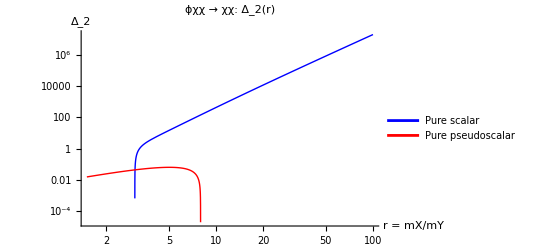

```mathematica
Print["\nDelta_2(r, lams, lamp) = ",Delta2];

(* ============================================================*)
(*Special cases*)
(* ============================================================*)
Print["\n--- Pure scalar coupling (lamp=0) ---"];
Delta2scalar=Delta2/. lamp->0//FullSimplify;
Print["Delta_2 = ",Delta2scalar];

Print["\n--- Pure pseudoscalar coupling (lams=0) ---"];
Delta2pseudo=Delta2/. lams->0//FullSimplify;
Print["Delta_2 = ",Delta2pseudo];

(* ============================================================*)
(*Numerical table*)
(* ============================================================*)
Print["\n===== Delta_2(r) for lams=1, lamp=0 ====="];
Print[PaddedForm[TableForm[Table[{r0,N[Delta2scalar/. {r->r0,lams->1},8]},{r0,{2,3,5,7,10,15,20,50,100}}],TableHeadings->{None,{"r = mX/mY","Delta_2"}}],{8,4}]];

Print["\n===== Delta_2(r) for lams=lamp ======"];
Print[PaddedForm[TableForm[Table[{r0,N[Delta2scalar/. {r->r0,lams->1,lamp->1},8]},{r0,{2,3,5,7,10,15,20,50,100}}],TableHeadings->{None,{"r = mX/mY","Delta_2"}}],{8,4}]];

Print["\n===== Delta_2(r) for lams=0, lamp=1 ====="];
Print[PaddedForm[TableForm[Table[{r0,N[Delta2pseudo/. {r->r0,lamp->1},8]},{r0,{2,3,5,7,10,15,20,50,100}}],TableHeadings->{None,{"r = mX/mY","Delta_2"}}],{8,4}]];

(* ============================================================*)
(*Plot*)
(* ============================================================*)
Plot[{Delta2scalar/. lams->1,Delta2pseudo/. lamp->1},{r,1.5,100},PlotRange->All,ScalingFunctions->{"Log","Log"},AxesLabel->{"r = mX/mY","Δ_2"},PlotLabel->"ϕχχ → χχ:  Δ_2(r)",PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->{"Pure scalar","Pure pseudoscalar"}]
```